## Lesson

An association:

```mathematica
<|a->1,b->2|>
```

<|a→1,b→2|>

Make association from list of rules:

```mathematica
Association[{a->1,b->2}]
```

<|a→1,b→2|>

Switch back to list of rules:

```mathematica
Normal[<|a->1,b->2|>]
```

{a→1,b→2}

Index association:

```mathematica
<|a->1,b->2|>[[-1]]
```

2

List keys of association:

```mathematica
Keys[<|a->1,b->2|>]
```

{a,b}

List values of association:

```mathematica
Values[<|a->1,b->2|>]
```

{1,2}

Sort association by keys:

```mathematica
KeySort[<|b->1,a->2|>]
```

<|a→2,b→1|>

Take elements with certain keys:

```mathematica
KeyTake[LetterCounts[WikipediaData["computers"]],Alphabet[]]
```

<|a→3674,b→624,c→2156,d→1591,e→5633,f→872,g→932,h→1707,i→3320,j→29,k→225,l→1977,m→1720,n→3240,o→3594,p→1330,q→63,r→3355,s→2895,t→4126,u→1560,v→447,w→537,x→96,y→717,z→44|>

Create association of number of appearances in list:

```mathematica
Counts[{a,a,b,a,b}]
```

<|a→3,b→2|>

Create association of number of appearances in string:

```mathematica
LetterCounts["aabab"]
```

<|a→3,b→2|>

## Questions

Q1. Make a list, in order, of the number of times each of the digits 0 through 9 occurs in 3^100.

```mathematica
Normal[KeySort[Counts[IntegerDigits[3^100]]]]
```

{0→7,1→9,2→9,3→5,4→1,5→5,6→4,7→7,9→1}

Q2. Make a labeled bar chart of the number of times each of the digits 0 through 9 occurs in 2^1000.

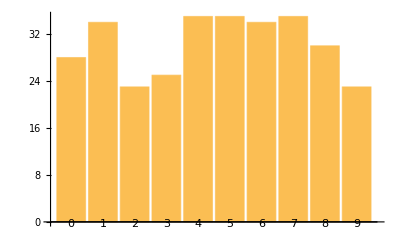

```mathematica
BarChart[KeySort[Counts[IntegerDigits[2^1000]]],ChartLabels->Automatic]
```

Q3. Make a labeled bar chart of the number of times each possible first letter occurs in words from WordList[ ].

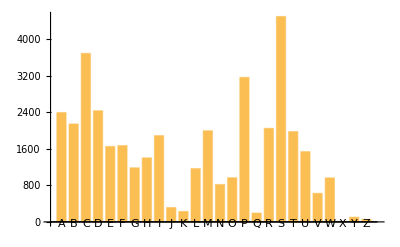

```mathematica
BarChart[Counts[ToUpperCase[StringTake[WordList[],1]]],ChartLabels->Automatic]
```

Q4. Make an association giving the 5 most common first letters of words in WordList[ ] and their counts.

```mathematica
ReverseSortBy[Counts[ToUpperCase[StringTake[WordList[],1]]],Value][[1;;5]]
```

<|S→4502,C→3694,P→3168,D→2436,A→2397|>

Q5. Find the numerical ratio of the number of occurrences of “q” and “u” in the Wikipedia entry for computers.

```mathematica
N[Count[Characters[WikipediaData["computers"]],"q"]/Count[Characters[WikipediaData["computers"]],"u"]]
```

0.0403846

Q6. Find the 10 most common words in ExampleData[{“Text”, “AliceInWonderland”}].

```mathematica
ReverseSortBy[Counts[TextWords[ExampleData[{"Text","AliceInWonderland"}]]],Value][[1;;5]]
```

<|the→573,and→319,a→269,to→248,she→203|>